```mathematica
(* Form of the wave function of a massive particle in a 2D flatland *)
ClearAll;
k=0.1;
A=1;
m=0;
n=4;
limit=BesselJZero[m,n];
ψ[r_,ϕ_, m_]:=A BesselJ[m,r]Exp[m*ϕ];
```

```mathematica
Plot[Abs[ψ[r,ϕ, m]]^2,{r,0,limit}, PlotRange->All]
RevolutionPlot3D[Abs[ψ[r,ϕ]]^2, {r,0,limit}, PlotRange->All, Boxed->False, Axes->{False,False,True},AxesLabel->{,,Style[Framed["|ψ(r,ϕ)|^2",FrameStyle->None,FrameMargins->20 ],Black,FontSize->48]}, TicksStyle->Directive[FontSize->48, Black], ImageSize->Large,ViewPoint->{45,45,45}]
```

-Graphics-

-Graphics3D-

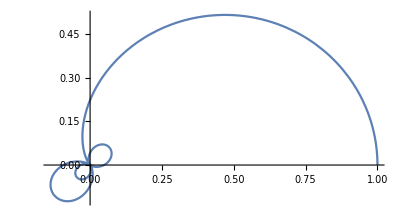

-Graphics3D-

```mathematica
PolarPlot[Abs[ψ[r,ϕ,m]]^2,{r,0,limit}]
RevolutionPlot3D[ψ[r,ϕ], {r,0,100}, PlotRange->All, Boxed->True, Axes->{False,False,True},PlotLabel->Style["ψ(r,ϕ)",Black,FontSize->48], TicksStyle->Directive[FontSize->48, Black], ImageSize->Large,ViewPoint->{10,10,5}]
```

```mathematica
Show[%593,ImageSize->Full]
```